GPU Accelerated Monte Carlo Simulation of High-Intensity Pulsed Laser-Electron Interaction

C F Nielsen
GPU Accelerated Monte Carlo Simulation of High-Intensity Pulsed Laser-Electron Interaction, Computer Physics Communications, 108425, doi: https://doi.org/10.1016/j.cpc.2022.108425.

Notebook: Óscar Amaro, June 2022,  @ GoLP-EPP

Abstract
“With an increasing interest in Strong Field QED (SFQED) effects during the past decade, in laser-electron interactions, comes a demand for more powerful and sophisticated simulation tools. In this paper we describe a numerical code (SFQED code) to simulate electrons colliding with a high intensity laser pulse where effects such as photon emission and pair production are included. This code simulates individual non-interacting particles which means that we are able to utilize the massive parallel computation capabilities of modern Graphics Processing Units (GPUs) to accelerate the propagation of many particles in parallel. Together with the SFQED code we present a separate code used to evaluate the Stratton-Chu vector diffraction integrals to be used with the SFQED code, allowing one to model the electromagnetic field at the focus given an arbitrary parabolic focusing mirror and an arbitrary incoming laser beam.”

## Integral of the form ∫∫ f(x,y) exp(i g(x,y)) dx dy

Examples where the method can be evaluated explicitly

```mathematica
Clear[ℐ1,ℐ2,f,g,x,y,xl,xu,yl,yu,p,k]
f[x,y]=1;
g[x,y]=1;

(* explicit integral *)
ℐ1=Integrate[f[x,y]Exp[I g[x,y]],{x,xl,xu},{y,yl,yu}]

(* ODE *)
psol=DSolve[D[D[p[x,y]Exp[I g[x,y]],x],y]==f[x,y]Exp[I g[x,y]],p[x,y],{x,y}][[1,1,2]]
(* evaluate function at boundaries *)
ℐ2=(psol Exp[I g[x,y]] /.{x->xu,y->yu})-(psol Exp[I g[x,y]] /.{x->xu,y->yl})-(psol Exp[I g[x,y]] /.{x->xl,y->yu})+(psol Exp[I g[x,y]] /.{x->xl,y->yl}) //Simplify

(* compare results *)
ℐ1-ℐ2//Simplify
```

ⅇ^ⅈ (-xl+xu) (-yl+yu)

x y+C[1][x]+C[2][y]

ⅇ^ⅈ (xl-xu) (yl-yu)

0

```mathematica
Clear[ℐ1,ℐ2,f,g,x,y,xl,xu,yl,yu,p,k]
f[x,y]=1;
g[x,y]=x+y;

(* explicit integral *)
ℐ1=Integrate[f[x,y]Exp[I g[x,y]],{x,xl,xu},{y,yl,yu}]

(* ODE *)
psol=DSolve[D[D[p[x,y]Exp[I g[x,y]],x],y]==f[x,y]Exp[I g[x,y]],p[x,y],{x,y}][[1,1,2]]
(* evaluate function at boundaries *)
ℐ2=(psol Exp[I g[x,y]] /.{x->xu,y->yu})-(psol Exp[I g[x,y]] /.{x->xu,y->yl})-(psol Exp[I g[x,y]] /.{x->xl,y->yu})+(psol Exp[I g[x,y]] /.{x->xl,y->yl}) //Simplify

(* compare results *)
ℐ1-ℐ2//Simplify
```

Integrate::pwrl: Unable to prove that integration limits {xl+yl,xu+yu} are real. Adding assumptions may help.

(ⅇ^(ⅈ xl)-ⅇ^(ⅈ xu)) (-ⅇ^(ⅈ yl)+ⅇ^(ⅈ yu))

-1+ⅇ^(-ⅈ x) C[1][y]+ⅇ^(-ⅈ y) C[2][x]

-((ⅇ^(ⅈ xl)-ⅇ^(ⅈ xu)) (ⅇ^(ⅈ yl)-ⅇ^(ⅈ yu)))

0

```mathematica
Clear[ℐ1,ℐ2,f,g,x,y,xl,xu,yl,yu,p,k]
f[x,y]=x+y;
g[x,y]=x+y;

(* explicit integral *)
ℐ1=Integrate[f[x,y]Exp[I g[x,y]],{x,xl,xu},{y,yl,yu}]

(* ODE *)
psol=DSolve[D[D[p[x,y]Exp[I g[x,y]],x],y]==f[x,y]Exp[I g[x,y]],p[x,y],{x,y}][[1,1,2]]
(* evaluate function at boundaries *)
ℐ2=(psol Exp[I g[x,y]] /.{x->xu,y->yu})-(psol Exp[I g[x,y]] /.{x->xu,y->yl})-(psol Exp[I g[x,y]] /.{x->xl,y->yu})+(psol Exp[I g[x,y]] /.{x->xl,y->yl}) //Simplify

(* compare results *)
Refine[ℐ1-ℐ2,{yl>0,yu>0,xl>0,xu>0}]//Simplify
```

Integrate::pwrl: Unable to prove that integration limits {xl+yl,xu+yu} are real. Adding assumptions may help.

-ⅇ^(ⅈ (xl+yl)) (ⅈ+xl)+ⅇ^(ⅈ (xl+yu)) (ⅈ+xl)+ⅇ^(ⅈ (xu+yl)) (ⅈ+xu)-ⅇ^(ⅈ (xu+yu)) (ⅈ+xu)+(-ⅇ^(ⅈ xl)+ⅇ^(ⅈ xu)) √(yl^2) Cos[yl]+(ⅇ^(ⅈ xl)-ⅇ^(ⅈ xu)) √(yu^2) Cos[yu]+Cos[yl] (-ⅈ Cos[xl]+ⅈ Cos[xu]+Sin[xl]-Sin[xu])+Cos[yu] (ⅈ Cos[xl]-ⅈ Cos[xu]-Sin[xl]+Sin[xu])+yl (-ⅈ Cos[xl]+ⅈ Cos[xu]+Sin[xl]-Sin[xu]) Sin[yl]+(Cos[xl]-Cos[xu]+ⅈ (Sin[xl]-Sin[xu])) Sin[√(yl^2)]+yu (ⅈ Cos[xl]-ⅈ Cos[xu]-Sin[xl]+Sin[xu]) Sin[yu]-(Cos[xl]-Cos[xu]+ⅈ (Sin[xl]-Sin[xu])) Sin[√(yu^2)]

-ⅇ^(-ⅈ x-ⅈ y) (2 ⅈ ⅇ^(ⅈ x+ⅈ y)+ⅇ^(ⅈ x+ⅈ y) x+ⅇ^(ⅈ x+ⅈ y) y-ⅇ^(ⅈ y) C[1][y]-ⅇ^(ⅈ x) C[2][x])

-ⅇ^(ⅈ (xl+yl)) (2 ⅈ+xl+yl)+ⅇ^(ⅈ (xu+yl)) (2 ⅈ+xu+yl)+ⅇ^(ⅈ (xl+yu)) (2 ⅈ+xl+yu)-ⅇ^(ⅈ (xu+yu)) (2 ⅈ+xu+yu)

0

## Figure 4: Analytical BW and CS spectrum

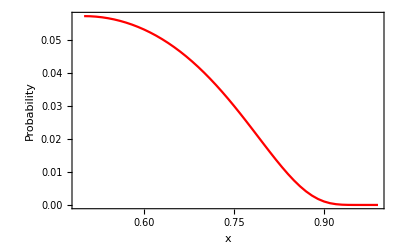

```mathematica
Clear[m,Eγ,w,x,ztil,χγ,α,dPpairdxdt,tab]
ztil=(1/(x(1-x))/χγ)^(2/3);
w=1/(x(1-x));
Eγ=1; (*normalized*)
α=m=1; (*normalized*)
χγ=1;

(* equation 26 *)
dPpairdxdt[x_]:=α (2m^2)/Eγ(NIntegrate[AiryAi[t],{t,(1/(x(1-x))/χγ)^(2/3),∞}]-AiryAiPrime[(1/(x(1-x))/χγ)^(2/3)](1/(x(1-x))-2)/(1/(x(1-x))/χγ)^(2/3))
tab=ParallelTable[{x,dPpairdxdt[x]},{x,0.5,0.99,0.01}];
ListPlot[tab,Joined->True,Frame->True,FrameLabel->{"x","Probability"},PlotStyle->Red]
```

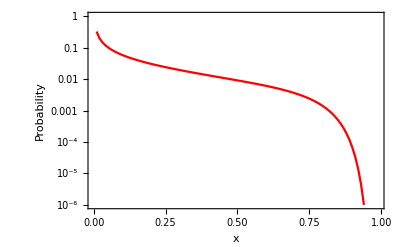

```mathematica
Clear[m,Em,w,u,ztil,χ,χγ,α,dPraddxdt,tab]

(*
dPraddudt=dPraddχγdt dχγdu
Solve[χγ==χ u/(1+u),u]
(D[χ u/(1+u),u]//Simplify)//.{u->χγ/(χ-χγ)}
*)
χ=1;
(* defined after equation 16 *)
z=(u/χ)^(2/3);
χγ=χ u/(1+u);
Em=20; (*normalized*)
α=1/137;
m=0.511 10^-3; (*normalized*)

(* equation 19 *)
dPraddxdt[u_]:=-α m^2/Em 1/(1+u)^2(NIntegrate[AiryAi[t],{t,(u/χ)^(2/3),∞}]+AiryAiPrime[(u/χ)^(2/3)]/(u/χ)^(2/3)(2+u^2/(1+u)))
tab=ParallelTable[{χγ,10^8.5(χ/(1+χγ/(χ-χγ))^2)^-1 dPraddxdt[χγ/(χ-χγ)]},{χγ,0.01χ,0.99χ,0.01}];
ListLogPlot[tab,Joined->True,Frame->True,FrameLabel->{"x","Probability"},PlotRange->{10^-6,10^0},PlotStyle->Red]
```

## Peak laser field of Standard Gaussian

```mathematica
Clear[x,y,z,r,W0,W,zR,EGauss,ϵ0,int1,int2,c]
W=W0 Sqrt[1+(z/zR)^2];

(* equation 10, without the oscillatory component *)
EGauss=E0 W0/W Exp[-r^2/W^2-2Log[2] z^2/(c^2 τ0^2)];

(* integrate first in r *)
int1=Integrate[ϵ0 r EGauss^2,{r,0,∞}]//Normal;
(* then integrate in z *)
int2=Refine[Integrate[int1,{z,-∞,+∞}]//Normal,{τ0>0,c>0}]

(* invert to get peak E0 field *)
E0peak = Solve[ℰL==int2,E0][[2,1,2]]//Simplify

(* compare with equation 32, with π instead of π^3 *)
Refine[E0peak-Sqrt[(8ℰL)/(W0^2 τ0 ϵ0 c)Sqrt[Log[2]/π]] //FullSimplify,{ϵ0>0,ℰL>0,W0>0,τ0>0,c>0}]
```

1/8 c E0^2 W0^2 ϵ0 τ0 √(π/Log[2])

(2 √2 √ℰL (Log[2]/π)^(1/4))/(√c W0 √ϵ0 √τ0)

0

## Peak laser field of Round Super Gaussian

```mathematica
Clear[x,y,z,r,W0,W,zR,ERound,ϵ0,int1,int2,c,n,ω]
W=W0 Sqrt[1+(z/zR)^2];

(* equation 33, extra factor of 1/2 because of sin^2 as explained in the text, and c factor because of integration in t *)
ERound=c/2 E0 W0/W Exp[-r^n/W^n]Exp[-2Log[2] t^2/τ0^2]/.{z->0};

(* integrate first in t *)
int1=Refine[Integrate[ϵ0 r ERound^2,{t,-∞,∞}]//Normal,{τ0>0}]
(* integrate then in r *)
int2=Refine[Integrate[int1,{r,0,∞}]//Normal,{W0>0,n>0}]
```

ⅇ^(-2 r^n W0^-n) E0^2 r ϵ0 τ0 √(π/Log[16])

2^(-(2+n)/n) E0^2 W0^2 ϵ0 τ0 Gamma[(2+n)/n] √(π/Log[16])

```mathematica
(* invert to get peak E0 field *)
E0peak = Solve[ℰL==int2,E0][[2,1,2]]//Simplify
```

(2^(1/2+1/n) √ℰL (Log[16]/π)^(1/4))/(W0 √ϵ0 √τ0 √Gamma[(2+n)/n])

```mathematica
(* compare with equation 35 *)
Refine[(E0peak-Sqrt[(2ℰL)/(W0^2 τ0 ϵ0 c)(2^(2/n) n)/Gamma[2/n] Sqrt[Log[2]/π]]) /.{ℰL->1,ϵ0->1,W0->1,τ0->1,c->1},{n>0}]//N
```

-0.68536 2.^(0.5 (1.+2./n)) √(n/Gamma[2./n])+(0.969246 2.^(0.5+1/n))/(√Gamma[(2.+n)/n])

## Peak laser field of Square Super Gaussian

```mathematica
Clear[nx,x,Wxnx,int,int2]
Refine[2 Integrate[Exp[-x^nx/Wx^nx],{x,0,∞}],{Wx>0,nx>0}]
```

2 Wx Gamma[1+1/nx]

```mathematica
int=Refine[,{x>0,nx>0,Wxnx>0}]
int2=(int/.{x->y,Wxnx->Wx^nx})-(int/.{x->-y,Wxnx->Wx^nx})//Simplify
```

```mathematica
Clear[x,y,z,r,W0,W,zR,ESquare,ϵ0,int1,int2,c,Wx,Wy,nx,ny]
W=W0 Sqrt[1+(z/zR)^2];
z=0;
(* equation 33 *)
ESquare=E0 Exp[-x^nx/Wx^nx-y^ny/Wy^ny];
(* integrate first in r *)
int1=Integrate[ϵ0  ESquare^2,{x,-∞,+∞}]//Normal
```

$Aborted

```mathematica
(* then integrate in z *)
int2=Refine[Integrate[int1,{y,-∞,+∞}]//Normal,{τ0>0}]
```

```mathematica
(* invert to get peak E0 field *)
E0peak = Solve[ℰL==int2,E0][[2,1,2]]//Simplify

(* compare with equation 35, with π instead of π^3 *)
Refine[E0peak-Sqrt[(2ℰL)/(W0^2 τ0 ϵ0 c)Sqrt[Log[2]/π]] //FullSimplify,{ϵ0>0,ℰL>0,W0>0,τ0>0,c>0}]
```

Part::partw: Part 2 of {} does not exist.

{}⟦2,1,2⟧

-(√2 √(ℰL/(c ϵ0 τ0)) (Log[2]/π)^(1/4))/W0+{}⟦2,1,2⟧